```mathematica
tetra[n_]:=n(n+1)(n+2)/6
tri[n_]:=n(n+1)/2
triple[m_,n_,l_]:=tetra[m+n+l]+tri[m+n]+m
```

```mathematica
untetra[z_]:=Block[{n=0},While[tetra[n]<=z,n++];n-1]
untri[z_]:=Block[{n=0},While[tri[n]<=z,n++];n-1]
untriple[z_]:=Block[{w,t,m},w = untetra[z];t=untri[z-tetra[w]];m=z-tri[t]-tetra[w];{m,t-m,w-t}]
```

```mathematica
toi[{m_,n_,l_}]:=triple[m,n,l]+1
fromi[d_]:=untriple[d-1]
```

```mathematica
k=7; M = tetra[k+1];
```

```mathematica
fromi/@Range[1,M] // Length
```

120

```mathematica
Subscript[T, r]=SparseArray[{{i_,j_}/;(fromi[i]-fromi[j] == {1,0,0}):>fromi[j][[1]],{i_,j_}/;(fromi[i]-fromi[j] == {-1,2,0}):>fromi[j][[1]],{i_,j_}/;(fromi[i]-fromi[j] == {0,1,0}):>-2 fromi[j][[1]]},{M,M}];
Subscript[T, λ] = SparseArray[{{i_,j_}/;(fromi[i]-fromi[j] == {0,1,0}):>fromi[j][[1]],{i_,j_}/;(fromi[i]-fromi[j] == {0,0,0}):>-fromi[j][[1]]},{M,M}];
Subscript[T, γ] = SparseArray[{{i_,j_}/;(fromi[i]-fromi[j] == {0,-1,1}):>fromi[j][[2]],{i_,j_}/;(fromi[i]-fromi[j] == {0,0,0}):>-fromi[j][[2]]},{M,M}];
```

```mathematica
P0 = ConstantArray[0,M];P0[[toi[{1,0,0}]]]=1;
```

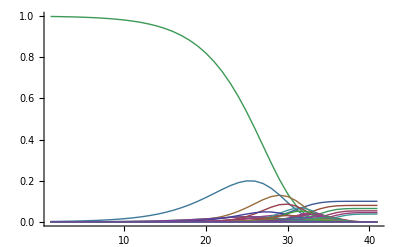

```mathematica
Table[MatrixExp[(0.25(0.1 Subscript[T, r]+Subscript[T, λ])+0.25 Subscript[T, γ]) 10^(k/10),P0],{k,-20,20}];
ListPlot[Transpose[%],Joined->True,PlotRange->All]
```

```mathematica
PDX[P_, {{mn_,l_},α_}]:=Sum[P[[toi[{m,mn-m,l}]]],{m,0,mn}]^α
```

```mathematica
TotalPDX[λ1_, r1_,γ1_,t_,data_]/;NumberQ[r1]:=Block[{P=MatrixExp[(λ1 (r1 Subscript[T, r]+Subscript[T, λ])+γ1 Subscript[T, γ]) t,P0]},Times@@(PDX[P,#]& /@ data)]
```

```mathematica
TotalPDX[0.25, 0.1,0.25, 3.0,{{{2,0},11},{{3,0},1},{{4,0},1}, {{1,1},4},{{2,1},3},{{4,1},1},{{6,1},1},{{0,2},6}, {{0,3},1}}]//Timing
```

{0.008001,6.51174×10^-41}

```mathematica
Prior=PDF[UniformDistribution[{1/10,9/10}],ρ]PDF[UniformDistribution[{1/100,1/2}],r];
```

```mathematica
{Z,ρ0,r0}=NIntegrate[{1,ρ,r} * TotalPDX[0.25, r,0.25 * ρ/(1-ρ), 3.0,{{{2,0},11},{{3,0},1},{{4,0},1}, {{1,1},4},{{2,1},3},{{4,1},1},{{6,1},1},{{0,2},6}, {{0,3},1}}] * Prior,{ρ,0.1,0.9},{r,0.01,0.5}]
```

$Aborted

```mathematica
Table[TotalPDX[0.25, r,0.25, 3.0,{{{2,0},11},{{3,0},1},{{4,0},1}, {{1,1},4},{{2,1},3},{{4,1},1},{{6,1},1},{{0,2},6}, {{0,3},1}}],{r,0,0.5,0.1}]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -5.25 with multiplicity 2.

Part::partw: Part 8 of MatrixExp[TagBox[SparseArray[Automatic, « 2 », {1, {{0, 0, « 117 », 251, 252}, « 1 »}, {3.` (0.25`  + 0.` _« 2 »), 3.` (-0.25` + 0.` _« 2 »), 0.75` (-1 + 0.` _« 2 »), 3.` (0.25`  + 0.` _« 2 »), « 43 », 3.` (0.5`  + 0.` _« 2 »), 3.` (-0.25` + 0.25` Plus[« 2 »]), 0.75` (2 + 0.` _« 2 »), « 202 »}}], False, Rule[Editable, False]], « 1 »] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -5.25 with multiplicity 2.

Part::partw: Part 9 of MatrixExp[TagBox[SparseArray[Automatic, « 2 », {1, {{0, 0, « 117 », 251, 252}, « 1 »}, {3.` (0.25`  + 0.` _« 2 »), 3.` (-0.25` + 0.` _« 2 »), 0.75` (-1 + 0.` _« 2 »), 3.` (0.25`  + 0.` _« 2 »), « 43 », 3.` (0.5`  + 0.` _« 2 »), 3.` (-0.25` + 0.25` Plus[« 2 »]), 0.75` (2 + 0.` _« 2 »), « 202 »}}], False, Rule[Editable, False]], « 1 »] does not exist.

Part::partw: Part 10 of MatrixExp[TagBox[SparseArray[Automatic, « 2 », {1, {{0, 0, « 117 », 251, 252}, « 1 »}, {3.` (0.25`  + 0.` _« 2 »), 3.` (-0.25` + 0.` _« 2 »), 0.75` (-1 + 0.` _« 2 »), 3.` (0.25`  + 0.` _« 2 »), « 43 », 3.` (0.5`  + 0.` _« 2 »), 3.` (-0.25` + 0.25` Plus[« 2 »]), 0.75` (2 + 0.` _« 2 »), « 202 »}}], False, Rule[Editable, False]], « 1 »] does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -5.25 with multiplicity 2.

General::stop: Further output of MatrixExp will be suppressed during this calculation.

$Aborted